## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Сучков А.Р. Группа: ТФ-13-22 Задача № 3

### -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[320,"Millimeters"],"Meters"];

r0=d0/2;L=Quantity[0.4,"Meters"];t0=Quantity[750,"DegreesCelsius"];tLiquid=Quantity[25,"DegreesCelsius"];α=Quantity[80,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[2659,("Kilograms")/("Meters")^3];
cp=Quantity[871,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[164,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[1.2,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

0.0000708121 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.0780488

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.097561

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.199159

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.127462

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении: -Graphics- Отдельно рассмотрим седьмой корень(определим его визуально с точностью е-5) -Graphics-

```mathematica
ϵ={0.3913 ,   3.8520   , 7.0267,   10.1811  , 13.3295,   16.4754   ,19.6198};
```

#### В вертикальном направлении: -Graphics- 7 корень: -Graphics-

```mathematica
μ={0.3074    ,3.1723    ,6.2987 ,   9.4351 ,  12.5741   ,15.7142 ,  18.8547  };
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

0.999064

```mathematica
tRadial[r_,τ_]=tLiquid+(t0-tLiquid)*ΘRadial[r,τ];
```

#### Найдем температуру на оси цилиндра в момент времени τ = 0 (оно тут показывает почему то бред но в расчетах далее это нормальные 1022К, можете сами прокомпилировать << tLiquid+(t0-tLiquid)*ΘRadial[0,0] >>)

```mathematica
tRadial[0,0]
```

295.838 K

#### Нормальное tRadial[0,0] а не как выше

```mathematica
tRadial[0,0]=tLiquid+(t0-tLiquid)*ΘRadial[0,0]
```

1022.47 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

749.321 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00026

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

1023.34 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

750.186 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.2 m | 689.638 °C
0.15 m | 702.76 °C
0.1 m | 710.312 °C
0.05 m | 713.828 °C
0. | 714.8 °C)

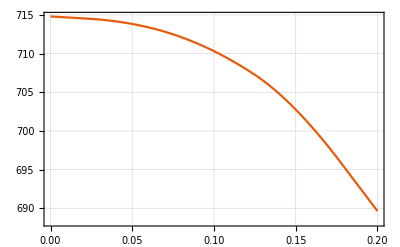

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.2 m | 663.918 °C
0.15 m | 676.532 °C
0.1 m | 683.791 °C
0.05 m | 687.171 °C
0. | 688.106 °C)

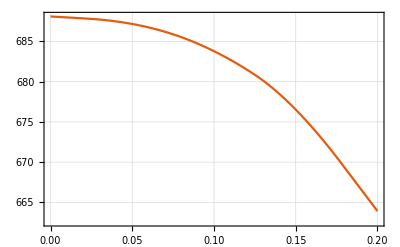

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.16 m | 688.106 °C
0.12 m | 699.552 °C
0.08 m | 707.928 °C
0.04 m | 713.065 °C
0. | 714.8 °C)

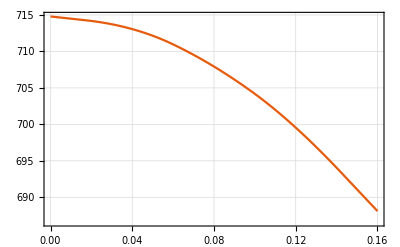

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.16 m | 663.918 °C
0.12 m | 674.946 °C
0.08 m | 683.017 °C
0.04 m | 687.966 °C
0. | 689.638 °C)

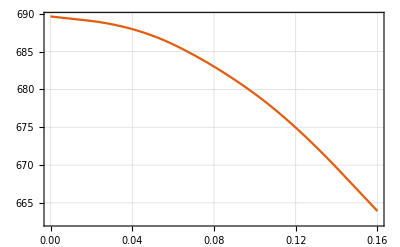

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}]//MatrixForm
```

(72. s | 714.8 °C
144. s | 688.223 °C
216. s | 661.264 °C
288. s | 634.948 °C
360. s | 609.595 °C
432. s | 585.261 °C
504. s | 561.932 °C
576. s | 539.571 °C)

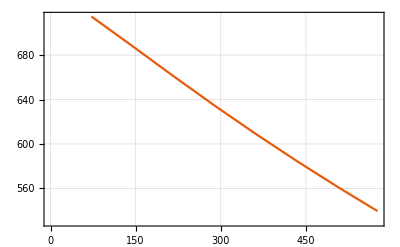

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}]//MatrixForm
```

(72. s | 704.956 °C
144. s | 679.096 °C
216. s | 652.525 °C
288. s | 626.571 °C
360. s | 601.566 °C
432. s | 577.567 °C
504. s | 554.558 °C
576. s | 532.505 °C)

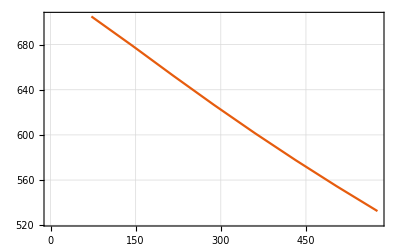

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[8]}]
```

{{72. s,6.5364},{144. s,6.49711},{216. s,6.45561},{288. s,6.41337},{360. s,6.37092},{432. s,6.3284},{504. s,6.28587},{576. s,6.24333}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[8]}]
```

{{72. s,6.52203},{144. s,6.48325},{216. s,6.44178},{288. s,6.39955},{360. s,6.35709},{432. s,6.31458},{504. s,6.27204},{576. s,6.22951}}

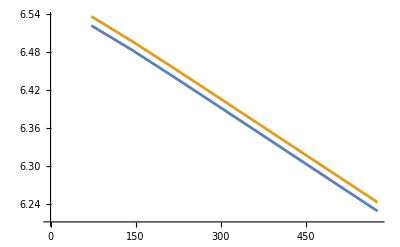

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии. регулярного режима гарантированно соответствует интервал [200,600] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3

```mathematica
FoRadialAt200=(a*Quantity[200,"Seconds"])/r0^2
```

0.553219

```mathematica
FoRadialAt600=(a*Quantity[600,"Seconds"])/r0^2
```

1.65966

```mathematica
FoVerticalAt200=(a*Quantity[200,"Seconds"])/(L/2)^2
```

0.35406

```mathematica
FoVerticalAt600=(a*Quantity[600,"Seconds"])/(L/2)^2
```

1.06218

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,200]/Θ3D[0,0,600]]/Quantity[600-200,"Seconds"]
```

0.000589443 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],200]/Θ3D[0,QuantityMagnitude[0.6*r0],600]]/Quantity[600-200,"Seconds"]
```

0.000589435 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.000589439 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.119854 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

0.0000706469 m^2/s

```mathematica
a
```

0.0000708121 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.00233291

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==1 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

5.40162×10^7 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.969546

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.98788

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.957795

```mathematica
Qτ1=Q(1-ΘAverage)
```

2.27974×10^6 J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
Show[ListLinePlot3D[Table[t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]],{x,0,L/2,L/4},{r,0,r0,r0/4}]],Boxed->False]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-

#### (покрутите поверхность :_) )